## This shows that there is definitely an optimal way to reconstruct a function. In particular, we should use Reconstruct over Reconstruct2 and plot it in the way that generates times5.

### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=If[l==-1,1,If[l==0,#,ϕ[2^l(#-2^-l(2i-1))]]]&
ϕ[lx_,ly_,i_,j_]:=ϕ[lx,i][#1]ϕ[ly,j][#2]&
ψ[lx_,ly_,i_,j_]:=ϕ[2^lx(#1-2^-lx i)]ϕ[2^ly(#2-2^-ly j)]&
ceil[x_,l_]:=If[x≥1,2^(l-1),1+Floor[2^(l-1)x]]
switch[x_]:=If[x≥1,x,1]
switch2[x_]:=If[x==-1,0,If[x==0,1,2^-x]]
switch3[x_,i_]:=If[x≤0,1,(-1)^(i+1)2^-x]

area[kx_]:=Which[kx==-1,1,kx==0,1/2,kx>0,2^-kx]

column2[diag_,row_]:=If[diag<1,diag, If[row<1,diag,diag-row+1]]
column1[diag_,row_]:=If[diag==row,-1,column2[diag,row]]

getrow[perp_,diag_]:=Which[diag==-1,-1,diag==0,Min[perp,0],perp≤diag,perp,True,diag]
getcol[perp_,diag_]:=Which[diag==-1,-1,diag==0,Min[diag-perp,0],perp> 0,diag-perp,True,diag]

endperp[n_]:=Which[n==-1,-1,n==0,1,True,n+1]

dϕ[x_]:=Which[Abs[x]>1,0,
			x==1 ,-1/2,
			x==-1,1/2,
			x==0,0,
			x>0,-1,
			True,1](* Don't think I need this*)
```

```mathematica
(*ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=(ϕ[2^l(#-2^-l(2i-1))]&)
ceil[x_]:=1+Floor[x]
dϕ[x_]:=If[Abs[x]>1,0,
			If[x==1 ,-1/2,
			If[x==-1,1/2,
			If[x==0,0,
			If[x>0,-1,1]]]]](* Don't think I need this*)


test[x_]:=Sin[Pi x]^2
dtest[x_]:=2 Pi Cos[Pi x] Sin[Pi x]*)
```

```mathematica
getCoefficient[f_,x_,l_]:=f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]
fullCoefficients[f_,l_]:={{f[1],f[0]}}~Append~Table[Table[getCoefficient[f,2^-k i,k],{i,1,2^k-1,2}],{k,1,l}]
Reconstruct2[coefficients_]:=coefficients[[1,1]]#+coefficients[[1,2]](1-#)+Sum[Sum[coefficients[[2,l,i]] ϕ[2^l(#-2^-l(2i-1))],{i,1,Length[coefficients[[2,l]]]}],{l,1,Length[coefficients[[2]]]}]&

Reconstruct[coefficients_]:=coefficients[[1,1]]#+coefficients[[1,2]](1-#)+Sum[coefficients[[2,l,ceil[#,l]]] ϕ[2^l(#-2^-l(2Ceiling[2^(l-1)#]-1))],{l,1,Length[coefficients[[2]]]}]&

Reconstruct3[coefficients_,x_]:=coefficients[[1,1]]x+coefficients[[1,2]](1-x)+Sum[coefficients[[2,l,ceil[x,l]]] ϕ[2^l(x-2^-l(2Ceiling[2^(l-1)x]-1))],{l,1,Length[coefficients[[2]]]}]
```

### Plot Times

```mathematica
times1=Table[Timing[Plot[Reconstruct[fullCoefficients[test,n]][x],{x,0,1}]][[1]],{n,1,8}]
times2=Table[Timing[Plot[Reconstruct2[fullCoefficients[test,n]][x],{x,0,1}]][[1]],{n,1,8}]
times3=Table[Timing[Plot[Reconstruct[fullCoefficients[test,n],x],{x,0,1}]][[1]],{n,1,8}]
times4=Table[Timing[Plot[(Reconstruct[#,x]),{x,0,1}]&[fullCoefficients[test,n]]][[1]],{n,1,12}]
times5=Table[Timing[Plot[(#[x]),{x,0,1}]&[Reconstruct[fullCoefficients[test,n]]]][[1]],{n,1,12}]
```

{0.014242,0.018775,0.058538,0.169928,0.40463,0.854566,1.77486,3.2545}

{0.014921,0.017087,0.066353,0.193866,0.465683,1.01602,2.14578,3.95112}

{0.009275,0.012194,0.014744,0.026384,0.052774,0.106637,0.21655,0.471713}

{0.007748,0.009628,0.008492,0.010215,0.013727,0.021311,0.037496,0.077803,0.15652,0.33775}

{0.010715,0.013727,0.020147,0.031694,0.040406,0.054859,0.076961,0.116685,0.180407,0.333275}

```mathematica
times4=Table[Timing[Plot[(Reconstruct[#,x]),{x,0,1}]&[fullCoefficients[test,n]]][[1]],{n,1,14}]
times5=Table[Timing[Plot[(#[x]),{x,0,1}]&[Reconstruct[fullCoefficients[test,n]]]][[1]],{n,1,14}]
```

{0.008208,0.009539,0.008986,0.010989,0.013745,0.023039,0.038354,0.071066,0.148901,0.303334,0.629705,1.24637,2.57357,5.11783}

{0.012202,0.012855,0.020835,0.037852,0.049373,0.059358,0.085875,0.122033,0.194481,0.333989,0.515664,0.760034,1.26565,2.22767}

```mathematica
times6=Table[Timing[Plot[(Reconstruct3[fullCoefficients[test,n],x]),{x,0,1}]][[1]],{n,1,8}]
```

{0.014725,0.01928,0.054579,0.171041,0.395112,0.847188,1.72671,3.24751}

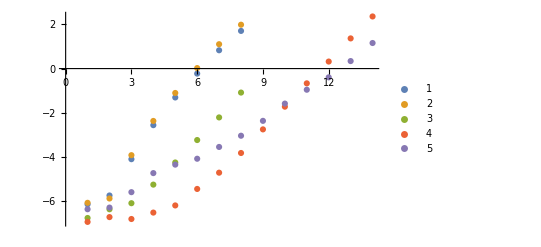

```mathematica
ListPlot[{times1,times2,times3,times4,times5}//Log2,PlotLegends->Automatic]
```